```mathematica
(* C3.AI COVID CHALLENGE *)
```

```mathematica
(* Sweden *)
```

```mathematica
(* Cases vs
```

```mathematica
pD0 = 0.6649;
pD1=0.1373;
pD2=0.0598;
pD3=0.1188;
pD4=0.0192;
```

```mathematica
(* COnditional Prob *)
```

```mathematica
pD0C6l1=0.7830;
pD1C6l1=0.9973;
pD2C6l1 = 0.9938;
pD3C6l1=0.9969;
pD4C6l1=0.9808;
```

```mathematica
pD0C6l0=1-pD0C6l1;
pD1C6l0=1-pD1C6l1;
pD2C6l0 =1-pD2C6l1;
pD3C6l0=1-pD3C6l1;
pD4C6l0=1-pD4C6l1;
```

```mathematica
(* C6 - 1 *)
```

```mathematica
prC6l0 = pD0 pD0C6l0 +  pD1 pD1C6l0+ pD2 pD2C6l0+ pD3 pD3C6l0+ pD4 pD4C6l0
```

0.145762

```mathematica
prC6l1= pD0 pD0C6l1 +  pD1 pD1C6l1+ pD2 pD2C6l1+ pD3 pD3C6l1+ pD4 pD4C6l1
```

0.854238

```mathematica
(* Quantum Prob *)
```

```mathematica
interfC6l0 = Sqrt[pD0 pD0C6l0 pD1 pD1C6l0]Cos[θ00-θ10]+ Sqrt[pD0 pD0C6l0  pD2 pD2C6l0] Cos[θ00-θ20] +  Sqrt[pD0 pD0C6l0  pD3 pD3C6l0] Cos[θ00-θ30]+ Sqrt[ pD0 pD0C6l0  pD4 pD4C6l0] Cos[θ00-θ40]+ 
pD1 pD1C6l0  pD2 pD2C6l0  Cos[θ10-θ20]+ pD1 pD1C6l0  pD3 pD3C6l0 Cos[θ10-θ30]+pD1 pD1C6l0  pD4 pD4C6l0 Cos[θ10-θ40]+
pD2 pD2C6l0  pD3 pD3C6l0  Cos[θ20-θ30]+ pD2 pD2C6l0  pD4 pD4C6l0 Cos[θ20-θ40]+pD3 pD3C6l0  pD4 pD4C6l0 Cos[θ30-θ40];
```

```mathematica
interfC6l1 = Sqrt[pD0 pD0C6l1 pD1 pD1C6l1]Cos[θ01-θ11]+ Sqrt[pD0 pD0C6l1 pD2 pD2C6l1] Cos[θ01-θ21] +  Sqrt[pD0 pD0C6l1  pD3 pD3C6l1] Cos[θ01-θ31]+ Sqrt[ pD0 pD0C6l1  pD4 pD4C6l1] Cos[θ01-θ41]+ 
pD1 pD1C6l1  pD2 pD2C6l1  Cos[θ11-θ21]+ pD1 pD1C6l1  pD3 pD3C6l1 Cos[θ11-θ31]+pD1 pD1C6l1 pD4 pD4C6l1 Cos[θ11-θ41]+
pD2 pD2C6l1  pD3 pD3C6l1  Cos[θ21-θ31]+ pD2 pD2C6l1  pD4 pD4C6l1 Cos[θ21-θ41]+pD3 pD3C6l1  pD4 pD4C6l1 Cos[θ30-θ41];
```

```mathematica
qprC6l0 = prC6l0 + 2 interfC6l0;
```

```mathematica
qprC6l1= prC6l1 + 2 interfC6l1;
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
(*FullSimplify[qprC6l1/(qprC6l0+qprC6l1)]; *)
```

```mathematica
Clear[θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41]
```

```mathematica
res = Maximize[{qprC6l0Norm,qprC6l0Norm+qprC6l1Norm == 1,θ00 >θ01,θ01>θ11},{θ00,θ01,θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41}]
```

{5.05316×10^14,{θ00→1.5657,θ01→1.49893,θ10→0.425229,θ20→0.0286994,θ30→0.0769387,θ40→-0.0589889,θ11→0.512242,θ21→0.167255,θ31→0.0814288,θ41→-0.0332004}}

```mathematica
(* Params *)
```

```mathematica
θ10=res[[2]][[3]][[2]];
 θ20=res[[2]][[4]][[2]];
 θ30=res[[2]][[5]][[2]];
θ40=res[[2]][[6]][[2]];
θ11=res[[2]][[7]][[2]];
θ21=res[[2]][[8]][[2]];
θ31=res[[2]][[9]][[2]];
θ41=res[[2]][[10]][[2]];
```

```mathematica
(* Updated probabilities *)
```

```mathematica
{qprC6l0Norm,qprC6l1Norm}
```

{(9.96469+3.89957 Cos[θ00]+0.459017 Sin[θ00])/(73.1371+3.89957 Cos[θ00]+102.901 Cos[θ01]+0.459017 Sin[θ00]+24.208 Sin[θ01]),1-(9.96469+3.89957 Cos[θ00]+0.459017 Sin[θ00])/(73.1371+3.89957 Cos[θ00]+102.901 Cos[θ01]+0.459017 Sin[θ00]+24.208 Sin[θ01])}

```mathematica
p0 = Plot3D[qprC6l0Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_00",16],Style["θ_01",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]]
```

-Graphics3D-

```mathematica
p1 = Plot3D[qprC6l1Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_00",16],Style["θ_01",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]]
```

-Graphics3D-

```mathematica
Show[p0,p1]
```

-Graphics3D-

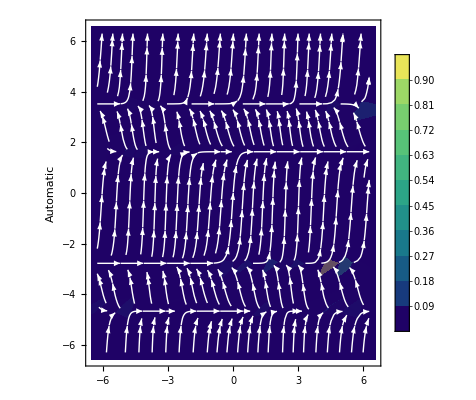

```mathematica
StreamDensityPlot[{qprC6l0Norm,qprC6l1Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

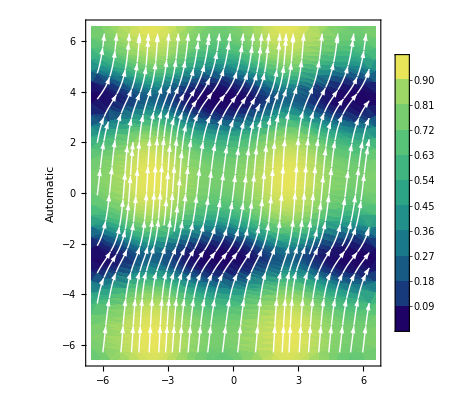

```mathematica
res = Maximize[{qprC6l0Norm,qprC6l0Norm+qprC6l1Norm == 1,θ00 >θ01},{θ00,θ01,θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41}]
```